# Warehouse Price Prediction

## Slide Show Subtitle

Baoxiang Pan
2017.5.1

## Data

```mathematica
SetDirectory["/Users/lambda/Documents/Code/Emma/Warehouse"];
data=Block[{tmt},tmt=Import["bj-0502.txt","Table"][[2;;]];Map[#[[{8,11,12,13,9}]]&,tmt]];
data=RandomSample[data];
data=Select[data,#[[5]]<4&];
input=Map[#[[{1,2,3,4}]]&,data];
output=Map[#[[5]]&,data];
mid=2000;
trainingset=input[[1;;mid]]->output[[1;;mid]];
testset=input[[mid+1;;]]->output[[mid+1;;]];
```

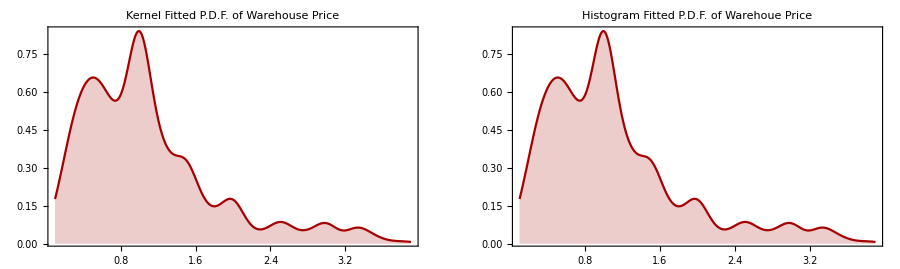

```mathematica
d1=SmoothKernelDistribution[output];
d2=HistogramDistribution[output];
GraphicsRow[{Plot[PDF[d1, x], {x, Min[output], Max[output]}, Frame -> True, PlotRange->Full,
Filling -> Axis,PlotLabel->"Kernel Fitted P.D.F. of Warehouse Price"],
Plot[PDF[d1, x], {x, Min[output], Max[output]}, Frame -> True, PlotRange->Full,
Filling -> Axis,PlotLabel->"Histogram Fitted P.D.F. of Warehoue Price"]},ImageSize->900]
```

## Prediction

```mathematica
Evaluation[model_]:=Block[{traininginput,trainingobservation,trainingprediction,
						   testinput,testobservation,testprediction,plot},
	traininginput=input[[1;;mid]];
	trainingobservation=output[[1;;mid]];
	testinput=input[[mid+1;;]];
	testobservation=output[[mid+1;;]];
	trainingprediction=Map[model,traininginput];
	testprediction=Map[model,testinput];
	plot[prediction_,observation_]:=ListPlot[Transpose[{prediction,observation}],
		PlotRange->Full,
		Frame->True,
		FrameLabel->{"prediction","observation"},
		PlotLabel->"r^2="<>ToString[(Correlation[prediction,observation])^2]<>"\nRMSE="<>
				  ToString[RMSE[prediction,observation]]];
	GraphicsRow[{plot[trainingprediction,trainingobservation],
	             plot[testprediction,testobservation]},ImageSize->1000]]
```

Linear Model

```mathematica
linear = Predict[trainingset, ValidationSet->testset,Method ->"LinearRegression"]
```

PredictorFunction[…]

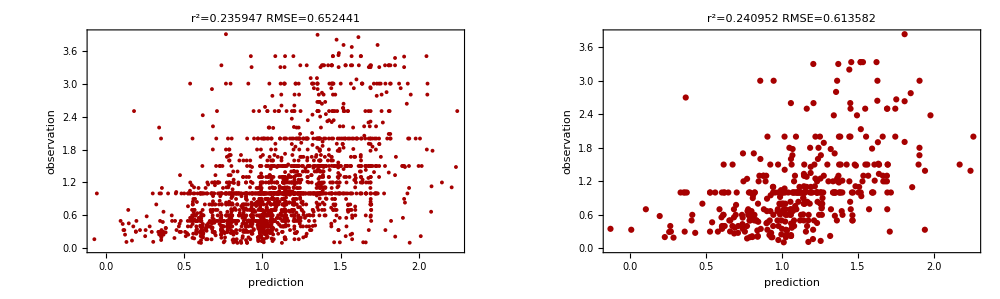

```mathematica
Evaluation[linear]
```

Nearest Neighbour

```mathematica
nn = Predict[trainingset, ValidationSet->testset,Method -> "NearestNeighbors"]
```

PredictorFunction[…]

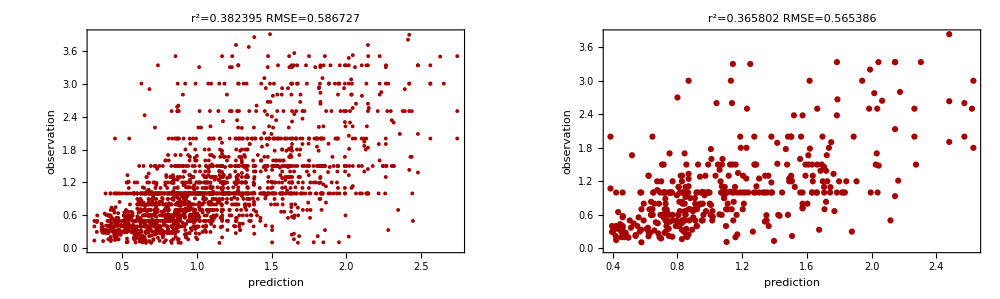

```mathematica
Evaluation[nn]
```

Random Forest

```mathematica
rf = Predict[trainingset, ValidationSet->testset,Method -> "RandomForest"]
```

PredictorFunction[…]

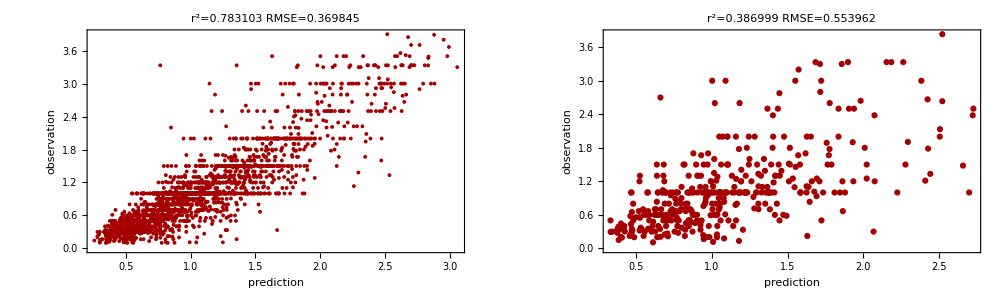

```mathematica
Evaluation[rf]
```

Gaussian Process

```mathematica
gp = Predict[trainingset, ValidationSet->testset, Method -> "GaussianProcess"]
```

PredictorFunction[…]

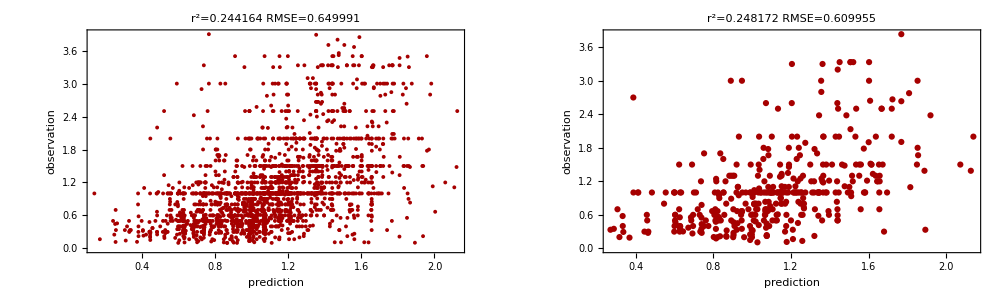

```mathematica
Evaluation[gp]
```

Neural Network

```mathematica
ann = Predict[trainingset,ValidationSet->testset, Method -> "NeuralNetwork"]
```

PredictorFunction[…]

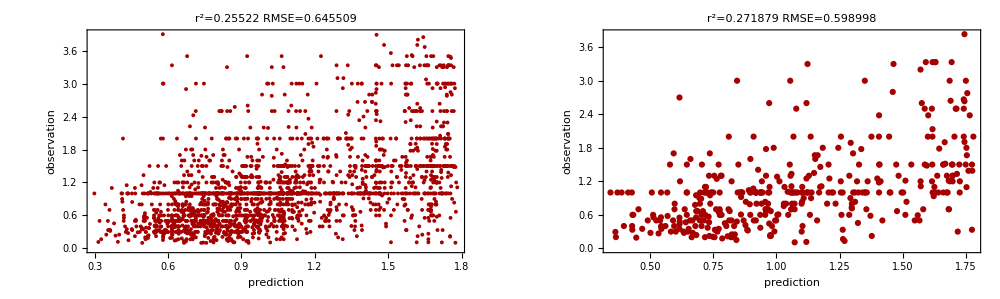

```mathematica
Evaluation[ann]
```